# Double copy root of Hawking thermality, comparative plot.

## [ doi: https://doi.org/10.1103/6gfs-kxbt ] [ arXiv:2511.01832 ]

JJ Carrasco, Yaxi Chen
carrasco@northwestern.edu

Notebook used to generate the publication version of the plot.

```mathematica
(*Set R=1*)
spectrumShape[λ_,C_]:=(C*λ/Sinh[Pi*C*λ])*Sqrt[1-λ^2];
```

```mathematica
cValues={1/2,2,5};
```

```mathematica
plotColors={(*French Blue*) RGBColor[{0,114,190}/256.],
                      (*Apple Green*)  RGBColor[{119,173,48}/256.], 
                      (*Vermilion*)   RGBColor[{228,67,51}/256.]};
```

```mathematica
plotStyles={(*Solid*)   {Thickness[0.005],Dashing[{}]},
                     (*Dotted*)  {Thickness[0.005],Dashing[{0.005,0.008}]} ,
                     (*Dashed*)  {Thickness[0.005],Dashing[{0.015,0.01}]}};
```

Here we normalize by dividing by max value, but we don' t have to hunt for it (!). For something this simple it's just multiplying by π .

```mathematica
Limit[spectrumShape[λ, c], λ -> 0] === 1/π
```

True

```mathematica
normalizedFunctions=π spectrumShape[λ,#]&/@cValues;
```

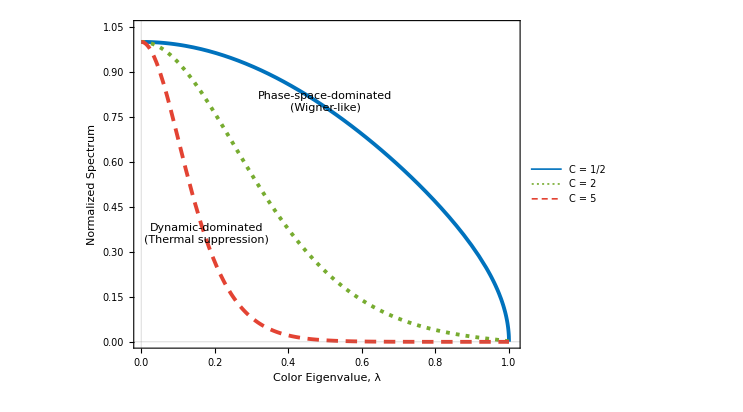

```mathematica
paperPlot=Plot[Evaluate[normalizedFunctions],{λ,0,1},(*Aesthetics and Framing*)
PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["Color Eigenvalue, λ",FontSize->18],Style["Normalized Spectrum",FontSize->18]},FrameTicksStyle->Directive[Black,16],PlotRange->{{0,1.01},{0,1.05}},ImageSize->550,AspectRatio->3/4,PlotStyle->Transpose[{plotColors,plotStyles}],PlotLegends->Placed[LineLegend["C = "<>ToString[#,TraditionalForm]&/@Rationalize[cValues],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&),LegendMarkerSize->30,LabelStyle->{FontSize->18}],{0.85,0.75} ],Epilog->{Text[Framed[Style["Phase-space-dominated\n(Wigner-like)",16,Black],Background->Opacity[1,White],FrameStyle->None,RoundingRadius->3],{0.5,0.8}],Text[Framed[Style["Dynamic-dominated\n(Thermal suppression)",16,Black],Background->Opacity[1,White],FrameStyle->None,RoundingRadius->3],{0.178,0.36}]}]
```

```mathematica
Export[NotebookDirectory[]~~"rootThermalityPlot.pdf",paperPlot];
```